## Initialization

Try to model exactly the solution for two cells

```mathematica
Clear["Global`*"];
```

```mathematica
S[x_]:= Coff +(Con-Coff)*x;
g[x1_,x2_]:= S[x1] + fd*S[x2];
```

Typical value of f(d):

```mathematica
fdval = Exp[R-a0]/a0 Sinh[R] /. {R-> 0.1, a0->1.5}
```

0.0164672

System parameters

```mathematica
params = {k-> 10 , fd-> fdval, n-> 2};
```

## Solutions with X_1=X_2, analytical solution (only n=1,2,3,4,5)

```mathematica
-(Subscript[C, on]-1)^2 X^3+[(Subscript[C, on]-1)^2 -2 (Subscript[C, on]-1)] X^2 + [2(Subscript[C, on]-1) - 1 - K^2/((1 + f(d))^2)]X + 1 =0
```

Fixed point equation 
 -(C_on-1)^2 X^3+[(C_on-1)^2 -2 (C_on-1)]X^2 + [2(C_on-1) - 1 - K^2/((1 + f(d))^2)]X + 1 =0

Δ = 18 a b c d - 4 b^3 d + b^2 c^2 - 4 a c^3 - 27 a^2 d^2;
Δ > 0: three distinct roots

```mathematica
a=  -(Con-1)^2;
b = (Con-1)^2 -2 (Con-1);
c =  2(Con-1) - 1 - k^2/((1 + fd)^2);
d = 1;
Δ = 18 a b c d - 4 b^3 d + b^2 c^2 - 4 a c^3 - 27 a^2 d^2;
Apart[Δ]
```

```mathematica
DensityPlot[ Sign[Δ /. params2] , {k,1,20},{Con,1,30},PlotLabel->"Bistability? Blue=no, yellow=yes", FrameLabel-> {"K", "C_ON"}]
```

## Full phase diagram

### Compute number of stable fixed points

Calculate fixed points

```mathematica
params2 = {k-> 10, Coff-> 1, Con-> 18, fd-> fdval, n-> 2};
nsol=NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. params2, {x1,x2}]
```

Calculate Jacobian matrix. General expression for eigenvalues is not useful.

```mathematica
J=FullSimplify/@{{D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x1],D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x2]},{ D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x1],D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x2]}};
J  // MatrixForm
```

Numerically calculate eigenvalues at the fixed points. Verify that they are stable (Re[λ] < 0 for all λ).

```mathematica
Jn =FullSimplify[J  /. params];
(* Show Jacobian*) TableForm@Table[ Jn /. nsol[[i]] // MatrixForm, {i, 1, Length[nsol]}]; 
ev=Table[ Eigenvalues[Jn  /. nsol[[i]]], {i, 1, Length[nsol]}];
Print["Eigenvalues: (λ1, λ2)=", MatrixForm/@ev ];
stability = MapThread[And, Transpose@Negative[ev]];
Print["Eigenvalues positive?"];
TableForm[stability, TableHeadings->{Table[StringReplace["Eigenvector number = %d", "%d" ->  ToString[i]], {i,1,Length[nsol]}], {"Positive?"}}]
```

Obtain the number of stable fixed points

```mathematica
nstable = Total[Boole/@stability];
Print["Number of stable fixed points = ", nstable];
```

### Modular function

```mathematica
allsol={};
nstablefunc[kin_,Conin_,fdin_, idx_]:=Module[{params2,nsol,J,Jn,ev,stability,tab,nstable},
Print["K = ", kin, ", Con= ", Conin, ", f(d)=", fdin];
params2 = {k-> kin, Coff-> 1, Con-> Conin, fd-> fdin, n-> 2};
nsol=NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. params2, {x1,x2}];
allsol[[idx]]=nsol;
J=FullSimplify/@{{D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x1],D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x2]},{ D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x1],D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x2]}};
Jn =FullSimplify[J  /. params2];
(* Show Jacobian*) TableForm@Table[ Jn /. nsol[[i]] // MatrixForm, {i, 1, Length[nsol]}]; 
ev=Table[ Eigenvalues[Jn  /. nsol[[i]]], {i, 1, Length[nsol]}];
(*Print["Eigenvalues: (λ1, λ2)=", MatrixForm/@ev ];*)
stability = MapThread[And, Transpose@Negative[ev]];
(*Print["Eigenvalues positive?"];
tab=TableForm[stability, TableHeadings->{Table[StringReplace["Eigenvector number = %d", "%d" ->  ToString[i]], {i,1,Length[nsol]}], {"Positive?"}}];
Print[tab];*)
nstable = Total[Boole/@stability];
Print["Number of stable fixed points = ", nstable];
nstable];
ndata =1;
allsol=Range[ndata];
nstablefunc[13, 30,fdval, 1]
```

K = 13, Con= 30, f(d)=0.0164672

Number of stable fixed points = 4

4

### Construct phase diagram

#### Example

```mathematica
Kall = {10, 15};
Conall = {15, 15};
fdall = {fdval, fdval};
ndata =Length[Kall];
allsol=Range[ndata];
MapThread[nstablefunc, {Kall, Conall, fdall, Range[ndata]}]
```

#### Full calculation

```mathematica
Klist = Range[1,20,1];
Conlist = Range[1,30,1];
Kall=Flatten[ConstantArray[Klist, {1,Length[Conlist]}]] ;
Conall=Flatten[Transpose[First@ConstantArray[Conlist, {1,Length[Klist]}]]];
fdall = Flatten[ConstantArray[fdval,{1,Length[Kall]}]];
ndata =Length[Kall];
allsol=Range[ndata];
data=MapThread[nstablefunc, {Kall, Conall, fdall, Range[ndata]}];
```

K = 1, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 1, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 2, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 3, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 4, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 5, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 6, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 7, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 8, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 9, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 10, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 11, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 12, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 13, f(d)=0.0164672

Number of stable fixed points = 4

K = 8, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 13, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 14, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 15, f(d)=0.0164672

Number of stable fixed points = 4

K = 9, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 15, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 16, f(d)=0.0164672

Number of stable fixed points = 2

K = 9, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 16, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 17, f(d)=0.0164672

Number of stable fixed points = 2

K = 9, Con= 17, f(d)=0.0164672

Number of stable fixed points = 4

K = 10, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 17, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 18, f(d)=0.0164672

Number of stable fixed points = 4

K = 10, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 18, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 19, f(d)=0.0164672

Number of stable fixed points = 2

K = 10, Con= 19, f(d)=0.0164672

Number of stable fixed points = 4

K = 11, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 19, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 20, f(d)=0.0164672

Number of stable fixed points = 2

K = 10, Con= 20, f(d)=0.0164672

Number of stable fixed points = 4

K = 11, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 12, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 20, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 21, f(d)=0.0164672

Number of stable fixed points = 2

K = 10, Con= 21, f(d)=0.0164672

Number of stable fixed points = 4

K = 11, Con= 21, f(d)=0.0164672

Number of stable fixed points = 4

K = 12, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 21, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 22, f(d)=0.0164672

Number of stable fixed points = 4

K = 11, Con= 22, f(d)=0.0164672

Number of stable fixed points = 4

K = 12, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 13, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 22, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 23, f(d)=0.0164672

Number of stable fixed points = 2

K = 11, Con= 23, f(d)=0.0164672

Number of stable fixed points = 4

K = 12, Con= 23, f(d)=0.0164672

Number of stable fixed points = 4

K = 13, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 23, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 24, f(d)=0.0164672

Number of stable fixed points = 2

K = 11, Con= 24, f(d)=0.0164672

Number of stable fixed points = 4

K = 12, Con= 24, f(d)=0.0164672

Number of stable fixed points = 4

K = 13, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 14, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 24, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 25, f(d)=0.0164672

Number of stable fixed points = 2

K = 11, Con= 25, f(d)=0.0164672

Number of stable fixed points = 4

K = 12, Con= 25, f(d)=0.0164672

Number of stable fixed points = 4

K = 13, Con= 25, f(d)=0.0164672

Number of stable fixed points = 4

K = 14, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 25, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 26, f(d)=0.0164672

Number of stable fixed points = 2

K = 11, Con= 26, f(d)=0.0164672

Number of stable fixed points = 2

K = 12, Con= 26, f(d)=0.0164672

Number of stable fixed points = 4

K = 13, Con= 26, f(d)=0.0164672

Number of stable fixed points = 4

K = 14, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 15, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 26, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 27, f(d)=0.0164672

Number of stable fixed points = 2

K = 12, Con= 27, f(d)=0.0164672

Number of stable fixed points = 4

K = 13, Con= 27, f(d)=0.0164672

Number of stable fixed points = 4

K = 14, Con= 27, f(d)=0.0164672

Number of stable fixed points = 4

K = 15, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 27, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 28, f(d)=0.0164672

Number of stable fixed points = 2

K = 12, Con= 28, f(d)=0.0164672

Number of stable fixed points = 4

K = 13, Con= 28, f(d)=0.0164672

Number of stable fixed points = 4

K = 14, Con= 28, f(d)=0.0164672

Number of stable fixed points = 4

K = 15, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 16, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 28, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 29, f(d)=0.0164672

Number of stable fixed points = 2

K = 12, Con= 29, f(d)=0.0164672

Number of stable fixed points = 2

K = 13, Con= 29, f(d)=0.0164672

Number of stable fixed points = 4

K = 14, Con= 29, f(d)=0.0164672

Number of stable fixed points = 4

K = 15, Con= 29, f(d)=0.0164672

Number of stable fixed points = 4

K = 16, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 29, f(d)=0.0164672

Number of stable fixed points = 1

K = 1, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 2, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 3, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 4, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 5, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 6, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 7, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 8, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 9, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 10, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 11, Con= 30, f(d)=0.0164672

Number of stable fixed points = 2

K = 12, Con= 30, f(d)=0.0164672

Number of stable fixed points = 2

K = 13, Con= 30, f(d)=0.0164672

Number of stable fixed points = 4

K = 14, Con= 30, f(d)=0.0164672

Number of stable fixed points = 4

K = 15, Con= 30, f(d)=0.0164672

Number of stable fixed points = 4

K = 16, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 17, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 18, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 19, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

K = 20, Con= 30, f(d)=0.0164672

Number of stable fixed points = 1

Find low and high fixed points

Important: set threshold θ for defining whether state is “low” or “high”

```mathematica
θ = 0.5 (*Threshold*)
Length/@({x1,x2}/.allsol);
allboole=Map[(#>θ)&, ({x1,x2}/.allsol),{3}];
data2= data;
For[i=1, i≤ Length[allsol], i++, 
If[
Length[allboole[[i]]] == 1, (*If only one solution*)
data2[[i]]=Boole@First@Apply[(#1 && #2)&,  allboole[[i]], 2 ],(* Low or high solution? low=0, high=1 *)
data2[[i]]=data[[i]] (*Else bistability, denote as 2*)
];
]
```

0.5

Original plot

Scale data for colors. Not used.
ListDensityPlot also not used. Use ArrayPlot instead.

```mathematica
datavalsscaled=(datavals-Min[datavals])/(Max[(datavals-Min[datavals])]);
colors = ColorData["TemperatureMap"]/@datavalsscaled;
SwatchLegend[colors,datavals];
ListDensityPlot[Transpose[{Kall, Conall, data}], InterpolationOrder->0, ColorFunction->colors,PlotLegends-> legend,PlotLabel->"Number of stable fixed points", FrameLabel-> {"K", "C_ON"}, BaseStyle->{FontSize-> 20}, ImageSize-> Large];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Manually set colors.

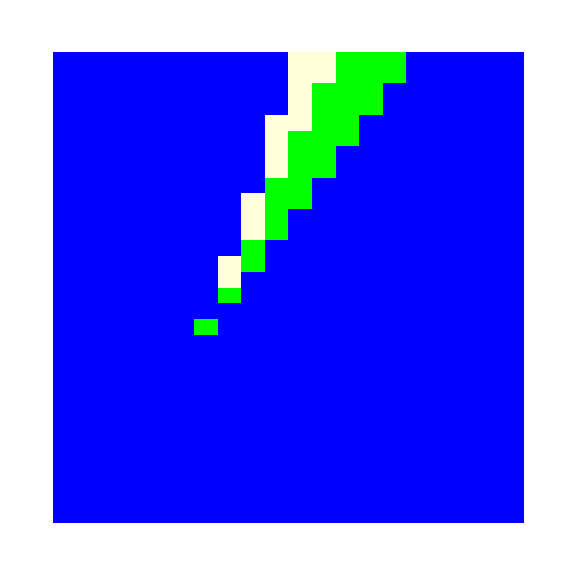

```mathematica
datavals=Union[data];
nelements =Length@datavals;
colors = {Blue, LightYellow, Green};
legend=SwatchLegend[colors,datavals]; (*{Style["1", 24],Style["2", 24]}*)
plot0=ArrayPlot[Partition[data,Length[Klist]],ColorRules->{1-> colors[[1]], 2-> colors[[2]], 4-> colors[[3]]}, FrameLabel-> {"C_ON", "K"}, PlotLegends -> None, BaseStyle->{FontSize-> 30}, DataReversed->True, FrameTicks-> {{{1,5, 10,15, 20, 25, 30}, None},{{1, 5, 10, 15,20}, None}}, AspectRatio->1,ImageSize-> Large]
```

New plot

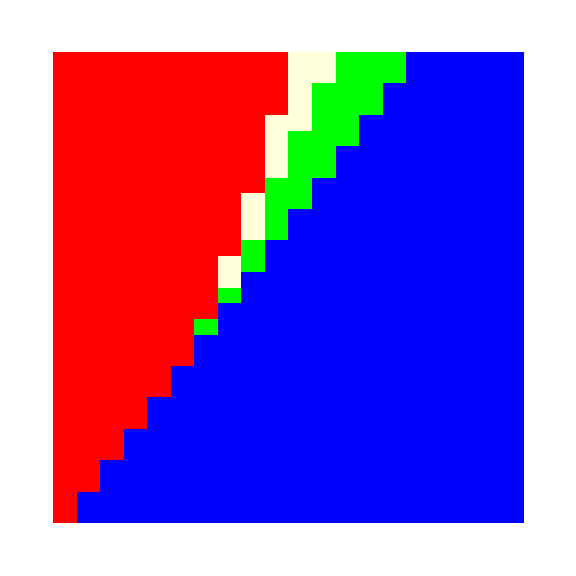

```mathematica
nelements =Length@Union[data2];
colors = {Blue,Red, LightYellow, Green};
legend=SwatchLegend[colors,{"Deact.", "Act.", "Act.-Deact."}];
plot0=ArrayPlot[Partition[data2,Length[Klist]],ColorRules->{0-> colors[[1]], 1-> colors[[2]], 2-> colors[[3]], 4-> colors[[4]]}, FrameLabel-> {"C_ON", "K"}, PlotLegends -> None, BaseStyle->{FontSize-> 30}, DataReversed->True, FrameTicks-> {{{1,5, 10,15, 20, 25, 30}, None},{{1, 5, 10, 15,20}, None}}, AspectRatio->1,ImageSize-> Large]
```

#### Export figure

```mathematica
name = "phase_diagram_n_2_strong_int_a0_0p5_Rcell_0p1_v1_new.pdf";
fname = FileNameJoin[{NotebookDirectory[], "finite_Hill_two_cells", name}];
Export[fname,plot0]
```

```mathematica
name = "phase_diagram_n_2_strong_int_a0_0p5_Rcell_0p1_v2_new";
fname = FileNameJoin[{NotebookDirectory[], "finite_Hill_two_cells", name}];
Export[StringJoin[fname, ".pdf"],plot1, "PDF", "ImageResolution"-> 300, "AllowRasterization"-> False]
Export[StringJoin[fname, ".eps"],plot1, "EPS", "ImageResolution"-> 300, "AllowRasterization"-> False]
```

## Dependence on a_0

Also construct a phase diagram for a_0